# Developing a Dynamic Network-Based Model for COVID-19

Christie Wilce, Ella Mattinen and Marcell Veiner

## Introduction & Background

Recently, there has been a significant uprise in epidemiological modelling, as a natural response to COVID-19 by the scientific community. Models of varying complexity and predictive power have been proposed, all with their unique set of implications and predictions. The reality of such models is that they are inherently imperfect, and are sensitive to the data they employ and the assumptions they are built on [6]. One typical assumption taken by many is that of a fixed or static model.

Consider the typical compartmental approach to epidemiological modelling, in which one usually starts by considering the basic Susceptible-Infected-Removed (SIR) model, which can definitely explain the fundamental behaviour of a disease (for example see [4; 14]), but fails to capture the response of society to it. As a result many approaches have tried extending the SIR model with different compartments to suit their needs [8]. The subdividing of these compartments can also be used to introduce basic demography to the modelled population, and parameters, such as the chance of infection or the recovery time can easily be tuned statistically so that the predictions match the observed data.

### Changing Circumstances

However, even complicated compartmental models [12] may fail to fit the data perfectly, and one possible explanation lies in the assumption the model is fixed over time. For example consider the number of cases in the UK during the early days. There is a steady rise in the number of new cases per day as the disease enters the country, which then levels off slightly after March 24th 2020, whereas many epidemic models would have predicted further spreading. What could have happened happened?

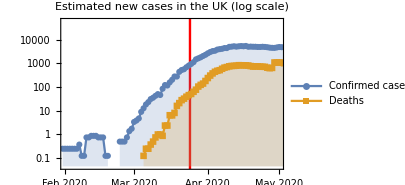

```mathematica
(* ResourceUpdate["Epidemic Data for Novel Coronavirus COVID-19"]; *)
DLLP=DateListLogPlot[ResourceData["Epidemic Data for Novel Coronavirus COVID-19","WorldCountries"][SelectFirst[#Country==Entity["Country","UnitedKingdom"]&],{"ConfirmedCases","Deaths"}][All,MovingAverage[Differences[#],Quantity[1,"Weeks"]]&],Sequence[PlotRange->{{{2020,2,1},{2020, 5, 1}},Automatic},PlotLegends->{"Confirmed cases","Deaths"},PlotLabel->"Estimated new cases in the UK (log scale)",Filling->{1->Bottom,2->Bottom},PlotMarkers->Automatic,ImageSize->300,PlotRange->Full],
Prolog->{Red,Rectangle[{{2020,3,24},-100},{{2020, 3, 25},100}]}]
```

Of course this could be due to several reasons, but a major factor was the introduction of the first lockdown here in the UK, which in turn changed the daily routines of people, and altered the spread of the disease. This also means that we need a different model from this point on, to cater for the new rules of society. Fortunately, a curated dataset of governmental measures is also available in Wolfram, although less frequently used by modellers. Looking at this brief list of measures, and their implementation dates, it is evident that any static model will fail to capture the spread of the pandemic in full.

```mathematica
measures = ResourceData[ResourceObject["Coronavirus COVID-19 Pandemic Government Measures"]][Select[#UNCode ===  "GBR"&],{"ImplementationDate","Category", "Measure", "Comments"}][SortBy["ImplementationDate"]]
```

Our goal with this simple study will be to propose a simple dynamic model which alters its constraints based on the measures dataset we have seen. Although this could also be done for compartmental models, considering its many variations, extensions and its inherent flaws regarding population homogeneity, we have decided to opt for a network (or agent-based) approach. The core of our approach is based on the excellent work of [18].

## Building the Model

The first step for any epidemiological model is to consider the pessimistic scenario where everyone gets infected in a small population. SIR models have a head start, as they do not directly model the population, but in our case we do need to come up with an appropriate representation. A great deal of work in network science has made sure that we have appropriate representations of social networks, and they are readily available in Wolfram.

#### Social Networks

#### Small Worlds

Our goal is to model the spread of an epidemic through a population where connections between people are random. There are many random graph models which would work in theory, however, we would like to choose one that has the properties of social networks. One characteristic of social network is the so called small-world property.  The small-world phenomenon, also known as six degrees of separation, has long fascinated the general public for its surprising statement that if you choose two individuals anywhere on Earth, you will find a path of at most six acquaintances between them. In the language of network science this is described through the average path length, which has to grow proportionally to the number of nodes, and the clustering coefficient, which has to be closer to 1 (than 0).

We can obtain a small-world from Watts-Strogatz random graphs. However,  if the probability of rewiring 𝓅 ≈ 0, then the Watts-Strogatz model gives a regular ring lattice, and if 𝓅 ≈ 1, we get a random graph that is similar to a binomial random graph. None of these cases posses the small-world property, and so choosing the correct 𝓅 in between these extremes is crucial. We replicate the following result from the original paper from Watts and Strogatz [17] which helped us in finding the right value for 𝓅.

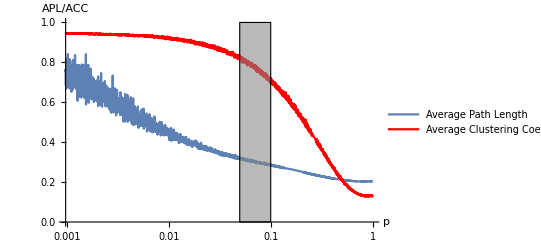

```mathematica
Show[LogLinearPlot[Mean[MeanGraphDistance /@RandomGraph[WattsStrogatzGraphDistribution[200,p,10],5]-1]/ (200/(4*10)),{p, 0,1},PlotLegends->LineLegend[{"Average Path Length"}], PlotRange->All, AxesLabel->{"p", "APL/ACC"},AxesOrigin->{0,0}],LogLinearPlot[Mean[MeanClusteringCoefficient /@ RandomGraph[WattsStrogatzGraphDistribution[200,p, 10], 5]]/ (0.75),{p, 0,1},PlotStyle->Red, PlotLegends->LineLegend[{"Average Clustering Coefficient"}], PlotRange->All, AxesLabel->{"p", "APL/ACC"},AxesOrigin->{0,0}],Graphics[{EdgeForm[Thin],GrayLevel[0.52,0.57],Rectangle[{-3,0},{-2.3,1}]}]]
```

From this we can conclude that a small value for 𝓅 is required for a small world graph. A value between 0.05 and 0.1 is recommended. In [18] 𝓅 is taken to be 0.1.

```mathematica
p = 0.075;
```

#### Network Demography

The immediate benefit of discrete approaches like this one, is the ability to represent a non-homogenous population. In this section we will quickly introduce simple demography to our model, by assigning each node an age. To make this more realistic, we will assign the age of a person so that the age distribution in our network is similar to that in real life. First let’s query the age distribution in the UK.

```mathematica
pop=Dataset[WolframAlpha["age distribution in UK",{{"AgeDistributionPyramidGraphic:AgeDistributionData",1},"ComputableData"}]];
agePop=QuantityMagnitude[Normal[pop[[All,2]]]+ Normal[pop[[All,3]]]];
dists=FindDistribution[RandomChoice[agePop->Range[2,102,5],10000 ],5];
```

After some workarounds we ask Wolfram to try and predict the distribution underlying our data. In fact, we ask for the first 5 of these, and select the most realistic one manually.

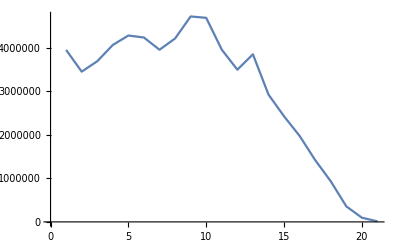

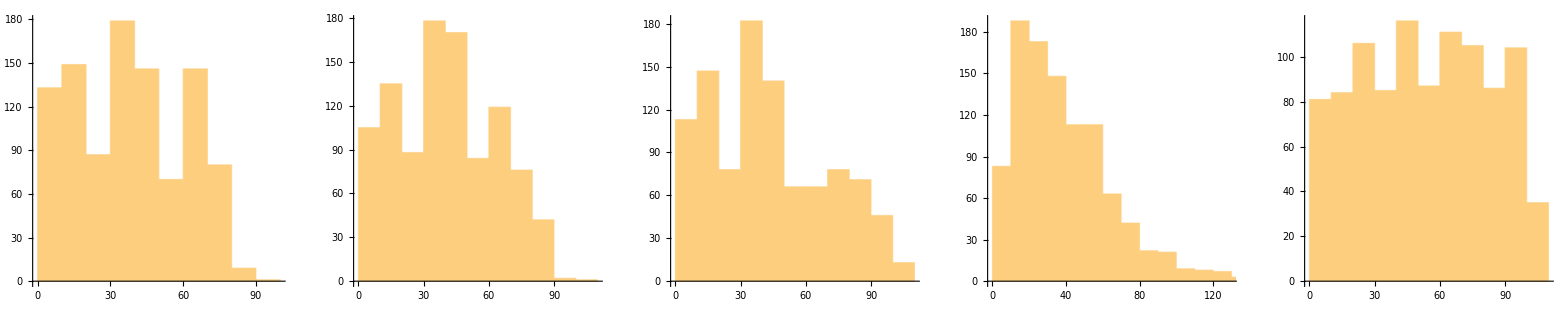

```mathematica
ListLinePlot[agePop]
GraphicsRow[Histogram[RandomVariate[dists[[#]],1000]] &/@Range[5]]
```

```mathematica
ageDist = dists[[4]]
```

PascalDistribution[2,0.0516504]

And so we have a distribution from which we can ask for a random variate and assign that as the age of a node.

Getting Infected

We have seen that we may approximate a random social network by a Watts-Strogatz Random Graph. We will start by generating a small community.

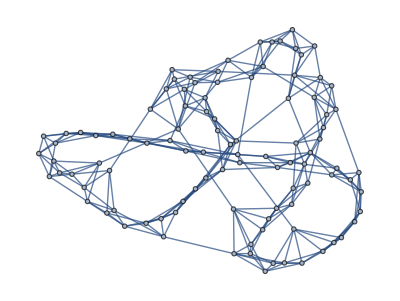

```mathematica
gBasic=RandomGraph[WattsStrogatzGraphDistribution[100,p,3]]
```

An important operation we will need is to obtain the friends or neighbours of a given person. The following function does that. We will also assume a random recovery time for each infected person. We will take the recovery time to be around 10 days [15].

```mathematica
avgRecovery = 10; 
agentNeighborhoods[g_]:=Merge[Catenate[
{#1->#2,#2->#1}&@@@EdgeList[g] (* Take every edge in g and create v -> u, u -> v *)
],                                                                   (* As we want v to be a neighbour of u and vica versa *)
Identity                                                                           (* Merge expects a merging function *)
]; 
recoveryTime =NormalDistribution[avgRecovery,3]; (* average recovery time around 10 days *) 
neighborsBasic=agentNeighborhoods[gBasic];
```

We then randomly select a portion of our population to be infected, and assign a recovery time to each infection. We will also distinguish between symptomatic and asymptomatic cases, for now let us just generate a few of each. Below the red nodes show symptoms but the yellow ones are asymptomatic.

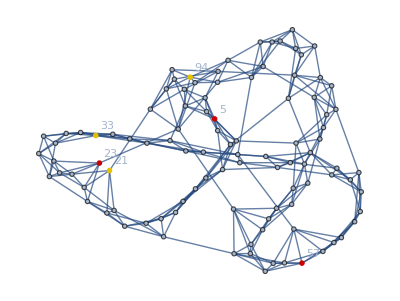

```mathematica
agentStates=Join[
AssociationMap[{Floor@RandomVariate[ageDist],"S",-1}&,Keys[neighborsBasic]], (* generate susceptibles *)
AssociationMap[{Floor@RandomVariate[ageDist],"Is",Floor@RandomVariate[recoveryTime]}&,RandomSample[Keys[neighborsBasic],3]], 
AssociationMap[{Floor@RandomVariate[ageDist],"Ia",Floor@RandomVariate[recoveryTime]}&,RandomSample[Keys[neighborsBasic],3]] (* generate infected *)
] ;
HighlightGraph[gBasic,{Keys@Select[agentStates,MatchQ[{_,"Is",_}]],Keys@Select[agentStates,MatchQ[{_,"Ia",_}]]}, VertexLabels->Automatic]
```

The virus also needs the chance to spread. We will have each person meeting with a subset of its friends, the number of which will be taken from the exponential distribution with   λ = 1 for now.

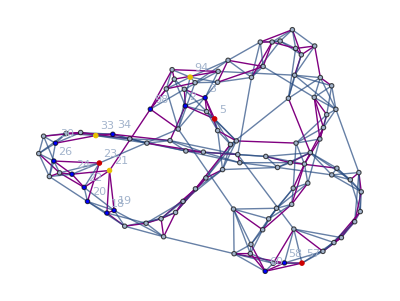

```mathematica
meetingCounts=AssociationThread[Keys[neighborsBasic],ExponentialDistribution[1]];
meetings=DeleteDuplicatesBy[
Flatten[
Function[
a,(* For each vertex a in all vertices *)
{a,#}&/@ (* Create a tuple (a, #) *)
RandomSample[ (* Where # is taken as *)
neighborsBasic[a],(* Take random neighbours of vertex a, but how many? *)
Clip[ (* A random number of them that is between 0 and #vertices *)
Round[RandomVariate[meetingCounts[a]]],
{0,Length[neighborsBasic[a]]}]
]
]/@Keys[neighborsBasic],1
],
Sort (* means that we delete duplicates {x, y} = {y, x}*)
];
agentMeetings=Merge[Catenate[{#1->#2,#2->#1}&@@@meetings],Identity]; (* same information but in dictionary *)

(* Define infected up here using With for convenience *)
With[{infected=Join[Keys@Select[agentStates,MatchQ[{_,"Is",_}]],Keys@Select[agentStates,MatchQ[{_,"Ia",_}]]]},
HighlightGraph[gBasic,{
Keys@Select[agentStates,MatchQ[{_,"Is",_}]],Keys@Select[agentStates,MatchQ[{_,"Ia",_}]],
Style[UndirectedEdge@@@meetings,Purple,Thick], 
Style[Complement[Flatten[Select[meetings,IntersectingQ[#,infected]&]],infected],Blue] 
},VertexLabels->Automatic
]
]
```

Above the blue nodes are meeting with infected and thus have a chance of becoming ill themselves. Next, we should update the states and see who gets infected. Diverging from our original source even more we will introduce a chance of infection.

Let us now consider the case that if a susceptible person meets with someone who is infected, there is a 60% chance for them to get infected.  This represents the secondary attack rate, which is defined as the probability that an infection occurs within a group after being exposed to an infected individual. This, however, is highly dependent on the environment and the nature of the meeting, thus we assume the nature of the meetings to be close contact, without precautionary actions in order to prevent infection. Here, the estimation has been derived from  a set of studies done on the transmission of COVID-19 where 0.6 represents the mean value taken from the transmission rate of infection from the following:

- Secondary attack rate and super-spreading events for SARS-CoV-2 [10]
- Transmission of COVID-19  [7]

These meetings consist of meals (mean 0.51), overnight camp (0.44) and choir (0.852). They are all forms of close contact meetings, where no precautionary actions were taken in order to prevent infection. When incorporating this into our model we have tested a few values for the chance of transmission, including 60% which is the average of the mentioned 3 figures, but we have found this too high. Instead we will set this to 40% as the model is more reliable and realistic in that case.

```mathematica
agentStates;
infectionRate = 0.4; symptomaticRate = 0.84;
AssociationMap[
Replace[
agentStates[#],
{
{n_,"S",m_}:>If[(MemberQ[Lookup[agentStates,agentMeetings[#]],{_,"Is",_}]||MemberQ[Lookup[agentStates,agentMeetings[#]],{_,"Ia",_}]) && RandomChoice[{infectionRate, 1-infectionRate}->{True, False}],
If[ RandomChoice[{symptomaticRate,1-symptomaticRate}->{True, False}],{n,"Is",Floor@RandomVariate[recoveryTime]},{n,"Ia",Floor@RandomVariate[recoveryTime]}],
{n,"S",m} ], (* If met with infected get infected 40% of the time *)
{n_,"Is",m_}:>If[m>0,{n,"Is",m-1},{n,"R",m}],(* Infected on the way to recovery *)
{n_,"Ia",m_}:>If[m>0,{n,"Ia",m-1},{n,"R",m}],(* Infected on the way to recovery *)
{n_,"R",m_}:>{n,"R",m}  (* Recovered stays recovered *)
}
]&,
Keys[agentStates]
];
```

We have also set 84% of the infected to show symptoms based on [5], and the rest to be asymptomatic. Putting this all together compactly we get the following:

```mathematica
runStep[agentStates_,neighbors_,meetingCounts_,recoveryTime_]:= (* function to advance simulation by one step *)Module[{meetings,agentMeetings}, (* For local scoping: meetings and agentMeetings won't be accessible in other cells *)meetings=DeleteDuplicatesBy[Flatten[Function[a,{a,#}&/@RandomSample[neighbors[a],Clip[Round[RandomVariate[meetingCounts[a]]],{0,Length[neighbors[a]]}]]]/@Keys[neighbors],1],Sort];
agentMeetings=Merge[Catenate[{#1->#2,#2->#1}&@@@meetings],Identity];
AssociationMap[Replace[agentStates[#],{{n_,"S",m_}:>If[(MemberQ[Lookup[agentStates,agentMeetings[#]],{_,"Is",_}]||MemberQ[Lookup[agentStates,agentMeetings[#]],{_,"Ia",_}]) && RandomChoice[{infectionRate, 1-infectionRate}->{True, False}],
If[ RandomChoice[{symptomaticRate,1-symptomaticRate}->{True, False}],{n,"Is",Floor@RandomVariate[recoveryTime]},{n,"Ia",Floor@RandomVariate[recoveryTime]}],
{n,"S",m} ],
{n_,"Is",m_}:>If[m>0,{n,"Is",m-1},{n,"R",m}],
{n_,"Ia",m_}:>If[m>0,{n,"Ia",m-1},{n,"R",m}],
{n_,"R",m_}:>{n,"R",m} 
}]&,Keys[agentStates]]]
```

```mathematica
simulateBasic[neighbors_,meetingCounts_,recoveryTime_,initialInfected_,maxSteps_:Infinity]:=Module[{agentStates,steps},
agentStates=Join[
AssociationMap[{Floor@RandomVariate[ageDist],"S",-1}&,Keys[neighbors]],
AssociationMap[{Floor@RandomVariate[ageDist],"Is",Floor@RandomVariate[recoveryTime]}&,RandomSample[Keys[neighbors],initialInfected]],
AssociationMap[{Floor@RandomVariate[ageDist],"Ia",Floor@RandomVariate[recoveryTime]}&,RandomSample[Keys[neighbors],initialInfected]]
];
steps=NestWhileList[runStep[#,neighbors,meetingCounts,recoveryTime]&,agentStates,MemberQ[{_,"Is",_}] ,1,maxSteps];
{steps, meetings}]
```

```mathematica
sirPlot[sim_,opts___]:=StackedListPlot[Transpose[sim],Frame->{{True,False},{True,False}},FrameLabel->{"Days","Agents"},opts]
```

Using a little animate or manipulate we can easily watch our network get infected.

```mathematica
resBasic= simulateBasic[neighborsBasic, meetingCounts, recoveryTime, 5];
simulationBasic = resBasic[[1]]; meetings = resBasic[[2]];
Manipulate[HighlightGraph[gBasic,{Keys@Select[Part[simulationBasic,step],MatchQ[{_,"Is",_}]], Style[Keys@Select[Part[simulationBasic,step],MatchQ[{_,"R",_}]], Black],Style[Keys@Select[Part[simulationBasic,step],MatchQ[{_,"Ia",_}]], Yellow]}], {step, 1, Length[simulationBasic], 1}]
```

Part::partd: Part specification simulationBasic⟦13⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::partd: Part specification simulationBasic⟦13⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::partd: Part specification simulationBasic⟦13⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

And see the typical graph of number of recovered, susceptible and infected animated over time animated.

```mathematica
numbersBasic = {Count[#,{_,"Ia",_}]+Count[#,{_,"Is",_}],Count[#,{_,"S",_}],Count[#,{_,"R",_}]}&/@simulationBasic;
Manipulate[sirPlot[numbersBasic[[;;step]],PlotLegends->{"Infected (Combined)","Susceptible","Recovered"}],{step, 1, Length[numbersBasic], 1}]
```

Part::take: Cannot take positions 1 through 33 in numbersBasic.

This already gives us a basic model to play with, and as we can see it produces the typical curves for each compartment that one can see in the relevant literature. Next we will focus on expanding on this model even more, by making it depend on the current restrictions.

## Making the Model Dynamic

A quick inspection of the Epidemic Data for Novel Coronavirus COVID-19 for UK tells us that we have data starting from March so we will pick that as a starting point. Let’s do something rather primitive, and convert the dates when government measures were introduced to simply the number of days passed since 01/02/2020. We then create an association between dates and the corresponding measures put in place that day.

```mathematica
dates = measures[All, "ImplementationDate"] // DeleteMissing //Normal;
noDays ={31,29,31,30,31,30,31,31,30,31,30,31};
noDays=(#["Month"]-2)*Part[noDays,#["Month"]]+(#["Day"])&/@dates;
categories =Select[measures, Not[MissingQ[#ImplementationDate]]&][All, "Category"]//Normal;
measuresDays = Merge[DeleteDuplicates]@Thread@Rule[noDays,categories]
```

<|42→{Public health measures},44→{Social and economic measures},47→{Public health measures,Social distancing},49→{Public health measures},51→{Social and economic measures,Social distancing},52→{Social distancing},53→{Social distancing},55→{Lockdown,Movement restrictions,Social distancing}|>

We are ignoring two columns (measure and comments), which also hold valuable information in this case, but in order to automate the process, and for the sake of this simple model, these will be ignored. A more pressing issue is that although the date of implementation is available for most of the measures in the dataset, the date on which they were lifted is not. We will proceed with the assumption that each restriction is enforced for 30 days only.

Furthermore, the actual effect of each restriction to the parameters of the model is unknown and so we will again have to resort to assumptions. We will assume that each restriction in the same category affects the corresponding parameters by the same amount. Thus we create lists for our parameters, with one value per day. Then we just have to adjust the model a bit to accommodate for this change.

```mathematica
Remove[meetings, meetingCounts]
meetingCounts[i_, neighbors_]:=AssociationThread[Keys[neighbors],ExponentialDistribution[α[[i]]]]; (* α defined later for conciseness *)
```

```mathematica
simulateDynamic[neighbors_,ageDist_,initialInfected_,maxSteps_:Infinity]:=Module[{agentStates,steps, day, meetings},
day=1;
agentStates=Join[
AssociationMap[{Floor@RandomVariate[ageDist],"S",-1}&,Keys[neighbors]],
AssociationMap[{Floor@RandomVariate[ageDist],"Is",Floor@RandomVariate[NormalDistribution[γ[[1]],3]]}&,RandomSample[Keys[neighbors],initialInfected]],
AssociationMap[{Floor@RandomVariate[ageDist],"Ia",Floor@RandomVariate[NormalDistribution[γ[[1]],3]]}&,RandomSample[Keys[neighbors],initialInfected]]
];
steps={};
While[(MemberQ[agentStates,{_,"Ia",_}]||MemberQ[agentStates,{_,"Is",_}])&&day≤maxSteps,
meetings=DeleteDuplicatesBy[Flatten[Function[a,{a,#}&/@RandomSample[neighbors[a],Clip[Round[RandomVariate[meetingCounts[day,neighbors][a]]],{0,Length[neighbors[a]]}]]]/@Keys[neighbors],1],Sort];
agentMeetings=Merge[Catenate[{#1->#2,#2->#1}&@@@meetings],Identity];
agentStates=AssociationMap[Replace[agentStates[#],{{n_,"S",m_}:>If[(MemberQ[Lookup[agentStates,agentMeetings[#]],{_,"Is",_}]||MemberQ[Lookup[agentStates,agentMeetings[#]],{_,"Ia",_}]) && RandomChoice[{β[[day]], 1-β[[day]]}->{True, False}],
If[ RandomChoice[{symptomaticRate, 1-symptomaticRate}->{True, False}],{n,"Is",Floor@RandomVariate[NormalDistribution[γ[[day]],3]]},{n,"Ia",Floor@RandomVariate[NormalDistribution[γ[[day]],3]]}],
{n,"S",m} ],
{n_,"Is",m_}:>If[m>0,{n,"Is",m-1},{n,"R",m}],
{n_,"Ia",m_}:>If[m>0,{n,"Ia",m-1},{n,"R",m}],
{n_,"R",m_}:>{n,"R",m} 
}]&,Keys[agentStates]];
day++;
AppendTo[steps,agentStates];
];
Return[steps]
]
```

Now let us convince ourselves that the restrictions do work and they have an effect on the spread of the virus.

```mathematica
g1=RandomGraph[WattsStrogatzGraphDistribution[1000,p,3]];neighbors1 = agentNeighborhoods [g1];
maxSteps = 1000;initialInfected=1; (* Ia, Is each*)
meetingMultiplier =1.2;infectionMultiplier=0.8; recoveryMultiplier=0.8;
λ=1.2;infectionRate=0.4;avgRecovery=10;effectDuration=30;
α = Table[λ,{i,maxSteps}];β = Table[infectionRate,{i,maxSteps}];γ=Table[avgRecovery,{i,maxSteps}];

res1= simulateDynamic[neighbors1,ageDist, initialInfected, maxSteps];
numbers1 = {Count[#,{_,"Ia",_}]+Count[#,{_,"Is",_}],Count[#,{_,"S",_}],Count[#,{_,"R",_}]}&/@res1;
p1= sirPlot[numbers1,PlotLegends->{"Infected","Susceptible","Recovered"},PlotLabel->"Without Restrictions"];

temp = Join[
Keys[Select[measuresDays,MemberQ[#,"Lockdown"]&]],
Keys[Select[measuresDays,MemberQ[#,"Movement restrictions"]&]]
];
For[i=1,i≤Length[temp],i++,
For[j=0,j<effectDuration &&temp[[i]]+j≤Length[α],j++,
α[[temp[[i]]+j]]*=meetingMultiplier;
];
]

temp = Join[
Keys[Select[measuresDays,MemberQ[#,"Social distancing"]&]],
Keys[Select[measuresDays,MemberQ[#,"Public health measures"]&]]
];
For[i=1,i≤Length[temp],i++,
For[j=0,j<effectDuration &&temp[[i]]+j≤Length[β],j++,
β[[temp[[i]]+j]]*=infectionMultiplier;
];
]

temp = Join[
Keys[Select[measuresDays,MemberQ[#,"Social and economic measures"]&]]
];
For[i=1,i≤Length[temp],i++,
For[j=0,j<effectDuration &&temp[[i]]+j≤Length[γ],j++,
γ[[temp[[i]]+j]]*=recoveryMultiplier;
];
]

res2= simulateDynamic[neighbors1,ageDist, initialInfected, maxSteps];
numbers2 = {Count[#,{_,"Ia",_}]+Count[#,{_,"Is",_}],Count[#,{_,"S",_}],Count[#,{_,"R",_}]}&/@res2;
p2 = sirPlot[numbers2,PlotLegends->{"Infected","Susceptible","Recovered"},PlotLabel->"With Restrictions"];

GraphicsRow[{p1, p2}]
```

-Graphics-

As we may observe the spread is directly affected by the restrictions, and although this model is still simple, it can sometimes produce the familiar second wave instead of a single peak, or simply a shorter one.

### Other Changes

With a working basis for our model, let us propose a few more extensions to make. We will discuss each addition individually, but for conciseness, the code will include all the changes at once.

### Reinfection

Although there is no consensus whether reinfection with the coronavirus [13] we would still like to add a small chance for recovered people to be susceptible again. We overwrite the same function as above, the original behaviour can still be achieved by feeding reinfectionRate = 0.

```mathematica
reinfectionRate =0.001;
```

### Death

Let us now consider the death rate of COVID-19. As this varies across ages, we use the age distribution to distinguish the death rate between different age groups. The values for these were taken from [1] with support of another study [16]. For example, the death rate for persons over the age of 80 was found to be 14.8% while for the younger population, age 10 to 39, it was found to be only 0.4%. But this is overall and not per day, so we should divide by the average number of infected days.

```mathematica
deathChance[m_] := Piecewise[{{0,9≥m},{0.002,39≥m≥10},{0.004,49≥m≥40},{0.013,59≥m≥50},{0.039,69≥m≥60},{0.08,79≥m≥70},{0.148,m≥80}}]/avgRecovery
```

### Vaccination

As vaccination is taken into consideration in our model, we must look at the rate at which the population gets vaccinated. Looking at the data provided by the UK Government [1], the average amount of daily 1st doses is around 300 000. If we take into account the 2nd doses, this average increases to 310 000, which accounts for 0.45% of the population. We will arbitrarily defined that vaccination starts after 60 days, this of course can be changed easily.

```mathematica
vaccinationRate=0.0045;vaccinationIntroduced = 60;
```

### Quarantine

It is also important to take into account the effect quarantine may have on the spread of the virus. Currently, the UK Government has advised individuals who suffer from any symptoms of the coronavirus to self-isolate for 10 days. Self-isolation measures are taken in order to prevent the spread of the virus, however, studies show [9] that individuals may be infectious 1-3 days prior to showing any symptoms. This also supports the claim that secondary infections may occur through transmission between an asymptomatic and a susceptible individual. Studies also show that symptomatic individuals are most infectious during the first 7 days after symptoms begin [15]. Hence, in our model we assume that after each symptomatic person has been in a 10 day quarantine, they are no longer infectious.  We will also assume that there is a 10 day lenient period after introducing the measure, where people go to quarantine gradually.

```mathematica
quarantiningIntroduced =30;maxdaysFree=7;mindaysFree=3;
```

```mathematica
lenientPeriod=10;lenient[day_,quarantiningIntroduced_]:=Piecewise[{{1,day>quarantiningIntroduced+ lenientPeriod},{Rescale[day, {quarantiningIntroduced, quarantiningIntroduced+lenientPeriod}],quarantiningIntroduced+ lenientPeriod≥day≥quarantiningIntroduced},{0,quarantiningIntroduced> day}}]
```

### Code For Changes

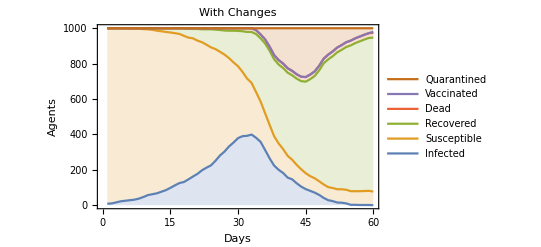

Part::partd: Part specification simulation2⟦18⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::partd: Part specification simulation2⟦18⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::partd: Part specification simulation2⟦18⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

```mathematica
simulateExtra[neighbors_,reinfectionRate_,vaccinationRate_,ageDist_,initialInfected_,maxSteps_:Infinity]:=Module[{agentStates,steps, day, meetings,toVaccinate},
day=1;
agentStates=Join[
AssociationMap[{Floor@RandomVariate[ageDist],"S",-1,-1}&,Keys[neighbors]],
AssociationMap[{Floor@RandomVariate[ageDist],"Is",Floor@RandomVariate[NormalDistribution[γ[[day]],3]],RandomInteger[{mindaysFree,maxdaysFree}]}&,RandomSample[Keys[neighbors],initialInfected]],
AssociationMap[{Floor@RandomVariate[ageDist],"Ia",Floor@RandomVariate[NormalDistribution[γ[[day]],3]],-1}&,RandomSample[Keys[neighbors],initialInfected]]
];
day=1;
steps={};
While[(MemberQ[agentStates,{_,"Ia",_,_}]||MemberQ[agentStates,{_,"Is",_,_}])&&day≤maxSteps,
meetings=DeleteDuplicatesBy[Flatten[Function[a,{a,#}&/@RandomSample[neighbors[a],Clip[Round[RandomVariate[meetingCounts[day, neighbors][a]]],{0,Length[neighbors[a]]}]]]/@Keys[neighbors],1],Sort];
agentMeetings=Merge[Catenate[{#1->#2,#2->#1}&@@@meetings],Identity];
agentStates=AssociationMap[Replace[agentStates[#],{{n_,"S",m_,l_}:>If[(MemberQ[Lookup[agentStates,agentMeetings[#]],{_,"Is",_,_}]||MemberQ[Lookup[agentStates,agentMeetings[#]],{_,"Ia",_,_}]) && RandomChoice[{β[[day]], 1-β[[day]]}->{True, False}],
If[ RandomChoice[{symptomaticRate, 1-symptomaticRate}->{True, False}],
{n,"Is",Floor@RandomVariate[NormalDistribution[γ[[day]],3]],RandomInteger[{mindaysFree,maxdaysFree}]},{n,"Ia",Floor@RandomVariate[NormalDistribution[γ[[day]],3]],l}
],
{n,"S",m,l}
],
{n_,"Is",m_,l_}:>If[RandomChoice[{deathChance[n],1-deathChance[n]}->{True,False}],{n,"D",m,-1},
If[m>0,If[day≥quarantiningIntroduced,
If[l<0&&RandomChoice[{lenient[day,quarantiningIntroduced],
1-lenient[day,quarantiningIntroduced]}->{True,False}],
{n,"Q",m-1,10},
{n,"Is",m-1,l-1}
],
{n,"Is",m-1,l}
],
{n,"R",m,l}
]
],
{n_,"Ia",m_,l_}:>If[m>0,{n,"Ia",m-1,l},{n,"R",m,l}],
{n_,"Q",m_,l_}:>If[l>0,{n,"Q",m-1,l-1},If[m>0,{n,"Is",m-1,l-1},{n,"R",m-1,l-1}]],
{n_,"R",m_,l_}:>If[ RandomChoice[{reinfectionRate, 1-reinfectionRate}->{True, False}],{n,"S",m,l},{n,"R",m,l}]
}]&,Keys[agentStates]];
toVaccinate = Take[Select[ReverseSortBy[First]@agentStates,Not[MemberQ[#,"V"]||MemberQ[#,"D"]]&],Ceiling[vaccinationRate*Length[agentStates]]];
agentStates=AssociationMap[Replace[agentStates[#],{
{n_,"D",m_,l_}:>{n,"D",m,l},
{n_,s_,m_,l_}:>If[day >= vaccinationIntroduced && s≠"D" &&MemberQ[Values[toVaccinate],{n,s,m,l}],{n,"V",m,l},{n,s,m,l}]
}]&,Keys[agentStates]];
day++;
AppendTo[steps,agentStates];
];
Return[steps]
]

g2=RandomGraph[WattsStrogatzGraphDistribution[1000,p,3]];neighbors2 = agentNeighborhoods [g2];
simulation2=simulateExtra[neighbors2, reinfectionRate,vaccinationRate,ageDist, 3, 100];
Manipulate[HighlightGraph[g2,{Style[Keys@Select[Part[simulation2,step],MatchQ[{_,"Is",_,_}]],Red], Style[Keys@Select[Part[simulation2,step],MatchQ[{_,"R",_,_}]], Black],
Style[Keys@Select[Part[simulation2,step],MatchQ[{_,"D",_,_}]], Pink],
Style[Keys@Select[Part[simulation2,step],MatchQ[{_,"V",_,_}]], Blue],
Style[Keys@Select[Part[simulation2,step],MatchQ[{_,"Q",_,_}]], Green],Style[Keys@Select[Part[simulation2,step],MatchQ[{_,"Ia",_,_}]], Red]}], {step, 1, Length[simulation2], 1}]
numbers2 = {Count[#,{_,"Ia",_,_}]+Count[#,{_,"Is",_,_}],Count[#,{_,"S",_,_}],Count[#,{_,"R",_,_}],Count[#,{_,"D",_,_}],Count[#,{_,"V",_,_}],Count[#,{_,"Q",_,_}]}&/@simulation2;
sirPlot[numbers2,PlotLegends->{"Infected","Susceptible","Recovered", "Dead","Vaccinated","Quarantined"},PlotLabel->"With Changes"]
```

### Communities

Returning to our main source for a brief moment, let us test our model on smaller communities loosely joint together. The following code taken from [18] creates a supergraph with random graph communities. We have adapted it so that it takes in the populations for each cluster, that is the number of nodes in the clusters. The old functionality is also supported, i.e. when population is a single number, each cluster will have that many nodes.

```mathematica
generateSupergraph[structure_,edgesSubgraph_,rewiring_,edgeThickness_,population_,scale_]:=
(* structure: supergraph, like a meshgraph 
  edgesSubgraph: the k parameter in Watts-Strogatz graph, i.e. number of neighbours / 2
  graphDistribution: the usualy random graph parameters
edgeThickness: number of edges connecting subgraphs
poulation: population for each community
scale: scaling factor for population
*)
Module[{clusters,g,previousCount=0,vertices,edges,connectingEdges, count=0,pop},
(* For compatibility, if population is only a number, create a list of it *)
pop=If[Length[population]>0, population, Table[population, VertexCount[structure]]];
clusters=Table[
Module[{cluster},
count +=1;(* for population indexing *)
cluster=IndexGraph[RandomGraph[WattsStrogatzGraphDistribution[Floor[pop[[count]]*scale], rewiring,edgesSubgraph]],previousCount];
previousCount+=VertexCount[cluster];
(* Above two lines create graph with vertices correctly indexed by numbers *)
(* Below line puts the vertices and edges of this graph in table *)
{VertexList[cluster],EdgeList[cluster]}],
(* For every node in the supergraph *)
{i,VertexCount[structure]}
];
(* 
	But clusters are {graph1, graph2, ...} 
   The line below converts this to {{all vertices}, {all edges}}
*)
{vertices,edges}=Union@@@Transpose[clusters];
(* Create random undirected edges connecting subclusters, first are the vertices hence composition *)
connectingEdges=UndirectedEdge@@RandomChoice@*First/@
clusters[[{#1,#2}]]& (* Gets the appropriate cluster *)
(* Creates edgeThicnkess number of copies of the mesh structure *)
@@@Catenate[ConstantArray[EdgeList[structure],edgeThickness]]; (* We will want to replace and add these edges to the graph *)
Graph[vertices,Join[edges,connectingEdges]]]
```

Let us first see that the code works in its original setting, we create a mesh like in [ https://community.wolfram.com/groups/-/m/t/1907703 ] with each community having 100 nodes.

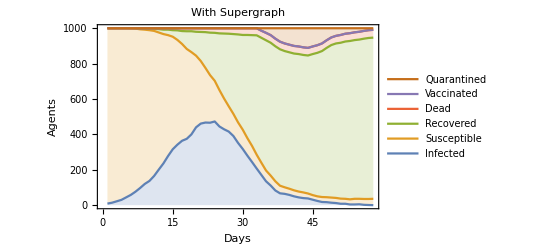

Part::partd: Part specification simulation3⟦50⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::partd: Part specification simulation3⟦50⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::partd: Part specification simulation3⟦50⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

```mathematica
g3 = generateSupergraph[IndexGraph@MeshConnectivityGraph@DelaunayMesh@RandomPoint[Disk[],10],5,p,10,100,1];
neighbors3 = agentNeighborhoods[g3];
simulation3=simulateExtra[neighbors3, reinfectionRate,vaccinationRate,ageDist, 3, 100];
Manipulate[HighlightGraph[g3,{Style[Keys@Select[Part[simulation3,step],MatchQ[{_,"Is",_,_}]],Red], Style[Keys@Select[Part[simulation3,step],MatchQ[{_,"R",_,_}]], Black],
Style[Keys@Select[Part[simulation3,step],MatchQ[{_,"D",_,_}]], Pink],
Style[Keys@Select[Part[simulation3,step],MatchQ[{_,"V",_,_}]], Blue],
Style[Keys@Select[Part[simulation3,step],MatchQ[{_,"Q",_,_}]], Green],Style[Keys@Select[Part[simulation3,step],MatchQ[{_,"Ia",_,_}]], Red]}], {step, 1, Length[simulation3], 1}]
numbers3 = {Count[#,{_,"Ia",_,_}]+Count[#,{_,"Is",_,_}],Count[#,{_,"S",_,_}],Count[#,{_,"R",_,_}],Count[#,{_,"D",_,_}],Count[#,{_,"V",_,_}],Count[#,{_,"Q",_,_}]}&/@simulation3;
sirPlot[numbers3,PlotLegends->{"Infected","Susceptible","Recovered", "Dead","Vaccinated","Quarantined"},PlotLabel->"With Supergraph"]
```

Now lets see if we can create a more realistic supergraph. We can query the largest cities in the UK, their location and population. We create a mesh using Delaunay Triangulation between cities, and feed this graph to the function we created. The result is a supergraph of smaller “cities” in the UK.

```mathematica
names=CityData[{Large,"UnitedKingdom"}];
citypop=QuantityMagnitude@ ( CityData[#,"Population"]& /@ names) ;
citycoords= CityData[#,"Coordinates"]& /@ names;
Needs["ComputationalGeometry`"]
dtri=DelaunayTriangulation[citycoords];
list={};Table[Do[AppendTo[list,{i, dtri[[All,2]][[i,j]]}],{j,1,Length[dtri[[All,2]][[i,All]]]}],{i,1,Length[dtri]}];
coupling=Table[0,{i,1,Length[names]},{j,1,Length[names]}];
For[i=1,i<Length[list]+1,i++, coupling[[list[[i]][[1]],list[[i]][[2]]]]=1;]
coupling=SparseArray[coupling];
```

To see things we need to tune things down a bit. Additionally the scaling factor can be used to scale down the population of each city by the same factor. This is required as this method cannot handle graphs of millions of nodes.

```mathematica
ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],2,p,2,citypop,0.0001];
ukNeighbors = agentNeighborhoods [ukSupergraph];
ukSimulation=simulateExtra[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 3, 10];
Manipulate[HighlightGraph[ukSupergraph,{Style[Keys@Select[Part[ukSimulation,step],MatchQ[{_,"Is",_,_}]],Red], Style[Keys@Select[Part[ukSimulation,step],MatchQ[{_,"R",_,_}]], Black],
Style[Keys@Select[Part[ukSimulation,step],MatchQ[{_,"D",_,_}]], Pink],
Style[Keys@Select[Part[ukSimulation,step],MatchQ[{_,"V",_,_}]], Blue],
Style[Keys@Select[Part[ukSimulation,step],MatchQ[{_,"Q",_,_}]], Green],Style[Keys@Select[Part[ukSimulation,step],MatchQ[{_,"Ia",_,_}]], Red]}], {step, 1, Length[ukSimulation], 1}]
```

Part::partd: Part specification ukSimulation⟦10⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::partd: Part specification ukSimulation⟦10⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

Part::partd: Part specification ukSimulation⟦10⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Keys::invrl: The argument Part[] is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

In order to scale up, however, we will have to make changes to the simulation. For example, for larger networks the manipulate is unfeasible, and so we will not store this information. The changes are below.

```mathematica
simulateComplete[neighbors_,reinfectionRate_,vaccinationRate_,ageDist_,initialInfected_,maxSteps_:Infinity]:=Module[{agentStates,steps, day, meetings,toVaccinate},
day=1;
agentStates=Join[
AssociationMap[{Floor@RandomVariate[ageDist],"S",-1,-1}&,Keys[neighbors]],
AssociationMap[{Floor@RandomVariate[ageDist],"Is",Floor@RandomVariate[NormalDistribution[γ[[day]],3]],RandomInteger[{mindaysFree,maxdaysFree}]}&,RandomSample[Keys[neighbors],initialInfected]],
AssociationMap[{Floor@RandomVariate[ageDist],"Ia",Floor@RandomVariate[NormalDistribution[γ[[day]],3]],-1}&,RandomSample[Keys[neighbors],initialInfected]]
];
steps={};
Monitor[
While[(MemberQ[agentStates,{_,"Ia",_,_}]||MemberQ[agentStates,{_,"Is",_,_}])&&day≤maxSteps,
meetings=DeleteDuplicatesBy[Flatten[Function[a,{a,#}&/@RandomSample[neighbors[a],Clip[Round[RandomVariate[meetingCounts[day, neighbors][a]]],{0,Length[neighbors[a]]}]]]/@Keys[neighbors],1],Sort];
agentMeetings=Merge[Catenate[{#1->#2,#2->#1}&@@@meetings],Identity];
agentStates=AssociationMap[Replace[agentStates[#],{{n_,"S",m_,l_}:>If[(MemberQ[Lookup[agentStates,agentMeetings[#]],{_,"Is",_,_}]||MemberQ[Lookup[agentStates,agentMeetings[#]],{_,"Ia",_,_}]) && RandomChoice[{β[[day]], 1-β[[day]]}->{True, False}],
If[ RandomChoice[{symptomaticRate, 1-symptomaticRate}->{True, False}],
{n,"Is",Floor@RandomVariate[NormalDistribution[γ[[day]],3]],RandomInteger[{mindaysFree,maxdaysFree}]},{n,"Ia",Floor@RandomVariate[NormalDistribution[γ[[day]],3]],l}],{n,"S",m,l}],{n_,"Is",m_,l_}:>If[RandomChoice[{deathChance[n],1-deathChance[n]}->{True,False}],{n,"D",m,-1},If[m>0,If[day≥quarantiningIntroduced,If[l<0&&RandomChoice[{lenient[day,quarantiningIntroduced],1-lenient[day,quarantiningIntroduced]}->{True,False}],{n,"Q",m-1,10},{n,"Is",m-1,l-1}],{n,"Is",m-1,l}],{n,"R",m,l}]],{n_,"Ia",m_,l_}:>If[m>0,{n,"Ia",m-1,l},{n,"R",m,l}],
{n_,"Q",m_,l_}:>If[l>0,{n,"Q",m-1,l-1},If[m>0,{n,"Is",m-1,l-1},{n,"R",m-1,l-1}]],
{n_,"R",m_,l_}:>If[ RandomChoice[{reinfectionRate, 1-reinfectionRate}->{True, False}],{n,"S",m,l},{n,"R",m,l}]
}]&,Keys[agentStates]];
day++;
AppendTo[steps,{Count[#,{_,"Ia",_,_}]+Count[#,{_,"Is",_,_}],Count[#,{_,"S",_,_}],Count[#,{_,"R",_,_}],Count[#,{_,"D",_,_}],Count[#,{_,"V",_,_}],Count[#,{_,"Q",_,_}]}&@agentStates];
 NotebookDelete[temp];
temp =PrintTemporary[sirPlot[steps,PlotLegends->{"Infected","Susceptible","Recovered", "Dead","Vaccinated","Quarantined"},PlotLabel->"UK Supergraph"]] 
];,Row[{ProgressIndicator[day,{1,maxSteps}],day}," "]
];
Return[steps]
]
```

Also make use of parallelization, and a progress indicator. Note that the experiments stops when no infected remain or when the time runs out. The indicator can only show the max number of days.

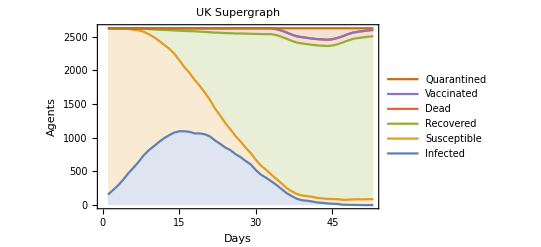

```mathematica
Parallelize[
numbers  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
sirPlot[numbers,PlotLegends->{"Infected","Susceptible","Recovered", "Dead","Vaccinated","Quarantined"},PlotLabel->"UK Supergraph"]
]
```

## Evaluation

```mathematica
Remove[numbers]
```

In order to gain better understanding of how our model works, we will compare how different parameters affect our UK Supergraph. The main three parameters we will compare are: quarantining at earlier and later dates; changes in infection rates; and changes in symptomatic rates. Once we get a better understanding of our model, our aim will be to see the similarities and differences between our UK supergraph and real UK data, pinpointing the limitations of our model and how to improve in the future.

#### Quarantine Introduced Earlier and Later

The first parameter we will evaluate is the introduction of quarantining. In our model, we have set ‘quarantineIntroduced=30’, so that at day 30, those who are symptomatic will be sent into isolation. In introducing quarantine earlier, we expect the curve of infection to flatten, so that the number of infections and deaths decrease. We will evaluate ‘quarantineIntroduced’ at day 15, 30 and 50.

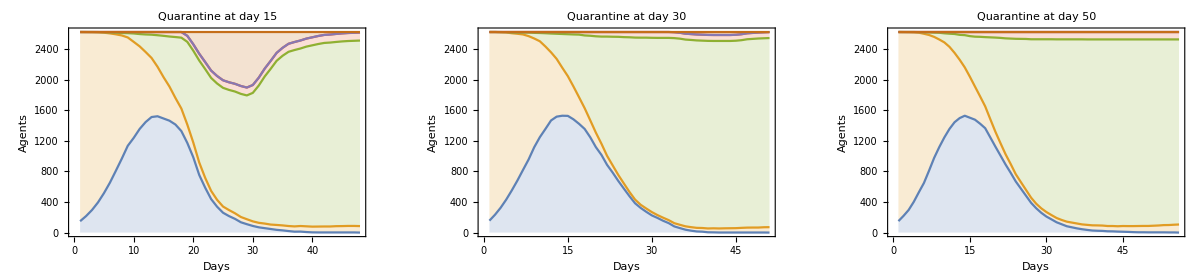

```mathematica
infectionRate=0.4;
symptomaticRate=0.84;

ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],3, p,10,citypop,0.0001];
ukNeighbors = agentNeighborhoods [ukSupergraph];

quarantiningIntroduced=15;
Parallelize[
numbers5  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
q1 =sirPlot[numbers5,PlotLabel->"Quarantine at day 15"];
];

quarantiningIntroduced=30;
Parallelize[
numbers6  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
q2 =sirPlot[numbers6,PlotLabel->"Quarantine at day 30"];
];

quarantiningIntroduced=50;
Parallelize[
numbers7  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
q3 =sirPlot[numbers7,PlotLabel->"Quarantine at day 50"];
];

GraphicsRow[{q1, q2, q3}]
```

A general observation we can make from these graphs, is that the later the quarantine is introduced, the higher the number of infected cases. However, due to quarantine being introduced after the spike of infections in the last two graphs, we cannot be certain this is in fact true. In order to fully visualise the effect, we would need to look at quarantine being introduced earlier than on day 30.

#### Change in Infection Rate

In our model, we have set ‘infectionRate=0.4’ so that for each meeting, if one person is infected, there will be a 40% the other will become infected. In increasing and decreasing the infection rate, the expectation would be for the number of people infected each day to decrease along with the number of deaths and for them to increase respectively. We will evaluate ‘infectionRate’ at 0.2, 0.4 and 0.8.

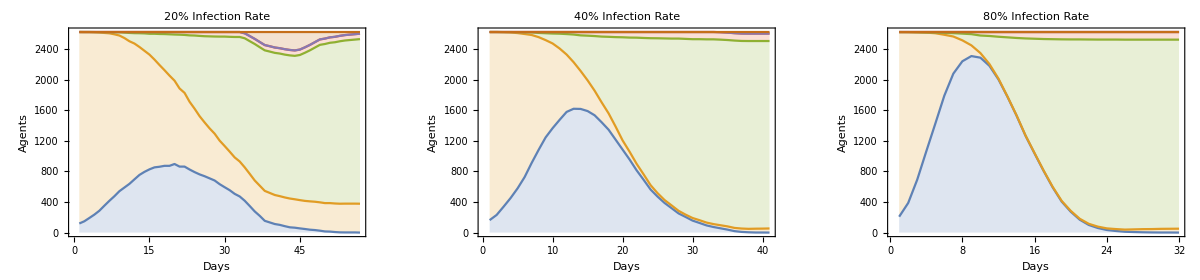

```mathematica
quarantiningIntroduced=30;ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5,p,10,citypop,0.0001];
ukNeighbors = agentNeighborhoods [ukSupergraph];
temp=Join[Keys[Select[measuresDays,MemberQ[#,"Social distancing"]&]],Keys[Select[measuresDays,MemberQ[#,"Public health measures"]&]]];

infectionRate=0.2;
β=Table[infectionRate,{i,maxSteps}];
For[i=1,i≤Length[temp],i++,For[j=0,j<effectDuration&&temp[[i]]+j≤Length[β],j++,β[[temp[[i]]+j]]*=infectionMultiplier;];]
Parallelize[
numbers11  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
i1=sirPlot[numbers11,PlotLabel->"20% Infection Rate"];
];

infectionRate=0.4;
β=Table[infectionRate,{i,maxSteps}];
For[i=1,i≤Length[temp],i++,For[j=0,j<effectDuration&&temp[[i]]+j≤Length[β],j++,β[[temp[[i]]+j]]*=infectionMultiplier;];]
Parallelize[
numbers12 =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
i2=sirPlot[numbers12,PlotLabel->"40% Infection Rate"];
];

infectionRate=0.8;
β=Table[infectionRate,{i,maxSteps}];
For[i=1,i≤Length[temp],i++,For[j=0,j<effectDuration&&temp[[i]]+j≤Length[β],j++,β[[temp[[i]]+j]]*=infectionMultiplier;];]
Parallelize[
numbers13 =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
i3=sirPlot[numbers13,PlotLabel->"80% Infection Rate"];
];

GraphicsRow[{i1,i2,i3}]
```

The graphs show that each time the infection rate doubles, the curve of infections steepens, resulting in a decrease in susceptible cases. However, in these graphs, we can see that there are few deaths, which could be a result of our death rate being too low. Therefore, the majority of infected cases become recovered. This mostly follows our expectations, as a larger infection rate generates an increase in infected cases and recovered cases, with a decrease in susceptible cases. Observing our graphs, we can see that quarantining only has an effect in the lower infection rates due to the flattened curve of infections. This is most likely caused by our ‘quarantineIntroduced’ parameter being too high with such a low population. The last two graphs finish too quickly due to the whole population becoming infected/recovered.

#### Change in Symptomatic Rate

In our model, when quarantine is introduced, ‘symptomatic’ cases are put into lock-down. Therefore, to look for the effects of increasing or decreasing the symptomatic rate, we need to observe what changes there are in quarantine. We have set ‘symptomaticRate=0.84’ in our model, in increasing or decreasing this parameter, we would expect the number of people quarantined to increase and decrease respectively. With a higher symptomatic rate, we would expect the curve of infection to flatten after quarantine is introduced. However, there should be no change in the number of infected cases before quarantine is introduced. We will evaluate ‘symptomaticRate’ at 0.4, 0.84 and 1.

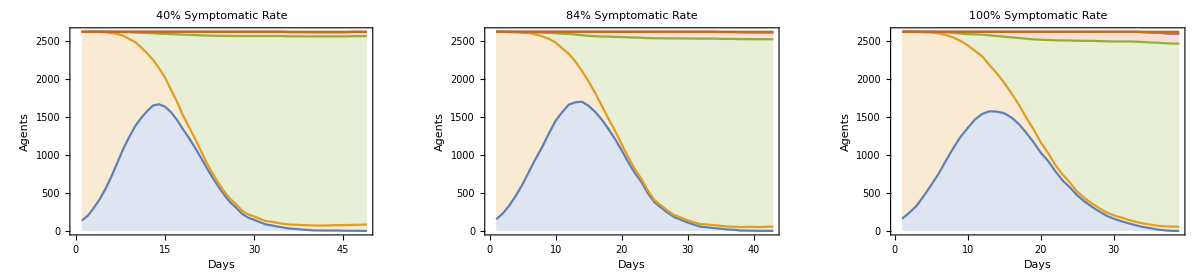

```mathematica
quarantiningIntroduced=30;infectionRate=0.4;symptomaticRate=0.84;
β=Table[infectionRate,{i,maxSteps}];
temp=Join[Keys[Select[measuresDays,MemberQ[#,"Social distancing"]&]],Keys[Select[measuresDays,MemberQ[#,"Public health measures"]&]]];
For[i=1,i≤Length[temp],i++,For[j=0,j<effectDuration&&temp[[i]]+j≤Length[β],j++,β[[temp[[i]]+j]]*=infectionMultiplier;];]
ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5,p,10,citypop,0.0001];
ukNeighbors = agentNeighborhoods [ukSupergraph];

symptomaticRate=0.4;
Parallelize[
numbers14  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
s1 =sirPlot[numbers14,PlotLabel->"40% Symptomatic Rate"];
]

symptomaticRate=0.84;
Parallelize[
numbers15  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
s2 =sirPlot[numbers15,PlotLabel->"84% Symptomatic Rate"];
]

symptomaticRate=1;
Parallelize[
numbers16  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
s3 =sirPlot[numbers16,PlotLabel->"100% Symptomatic Rate"];
]

GraphicsRow[{s1, s2, s3}]
```

Due to our current parameters, mainly the date quarantine is introduced, we cannot visualise the effect a change in symptomatic rate has on our model well. But it can be observed that if all infected show symptoms, the curve is more flat, as restrictions affect them more.

#### Change in Reinfection Rate

Another parameter we can look at is the reinfection rate. In our model we set ‘reinfectionRate=0.001’, so that if someone contracts COVID-19, instead of becoming recovered (or dead), they could instead become susceptible, resulting in a chance of reinfection. If the reinfection rate were to increase, we would expect an increase in the total infected cases, resulting in an increase in quarantined cases and deaths, and an increase in susceptible cases. We will evaluate ‘reinfectionRate’ at 0.001, 0.01 and 0.1.

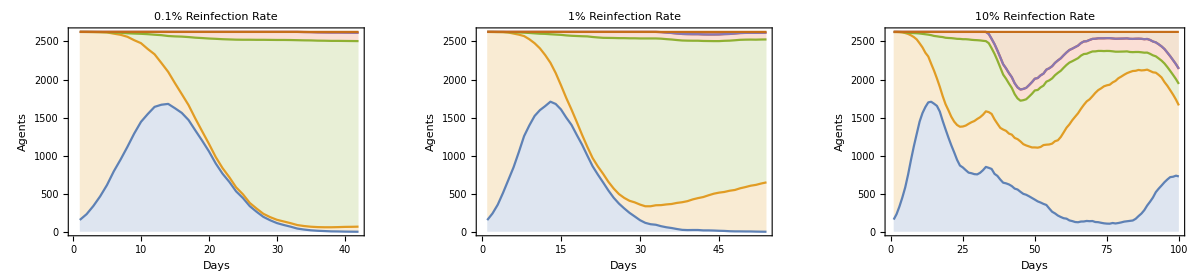

```mathematica
quarantiningIntroduced=30;infectionRate=0.4;
β=Table[infectionRate,{i,maxSteps}];
symptomaticRate=0.84;ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5,p,10,citypop,0.0001];
ukNeighbors = agentNeighborhoods [ukSupergraph];

Parallelize[
numbers17  =simulateComplete[ukNeighbors, 0.001,vaccinationRate,ageDist, 50, 100];
r1 =sirPlot[numbers17,PlotLabel->"0.1% Reinfection Rate"];
]

Parallelize[
numbers18  =simulateComplete[ukNeighbors, 0.01,vaccinationRate,ageDist, 50, 100];
r2 =sirPlot[numbers18,PlotLabel->"1% Reinfection Rate"];
]

Parallelize[
numbers19  =simulateComplete[ukNeighbors, 0.1,vaccinationRate,ageDist, 50, 100];
r3 =sirPlot[numbers19,PlotLabel->"10% Reinfection Rate"];
]

GraphicsRow[{r1,r2,r3}]
```

The general observation we can make, is that as the reinfection rate grows, the amount of susceptible cases grows. However, when we reach a higher reinfection rate, such as 0.1, there are many differences when compared with the lower rates. We can expect that as the infection spreads and the number of susceptible cases decrease, there will be a higher number of people in quarantine, flattening the curve and lowering the infected cases. However, with a higher rate of reinfection, the number of susceptible cases begins to increase, resulting in a second wave of infection. Due to the model only allowing 100 steps, the final graph ends with a second wave beginning. However, we can expect this graph to continue with the same pattern stated above.

3x3 Graph Showing the Effect of Changing the Parameters

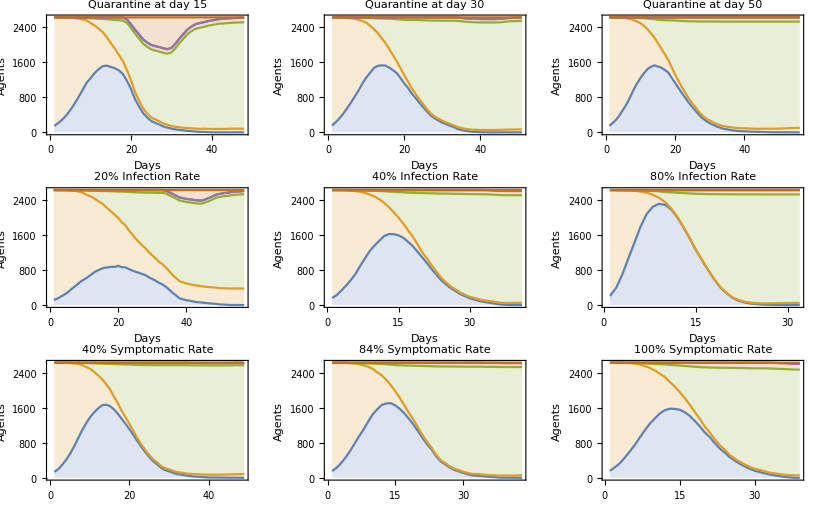

```mathematica
GraphicsGrid[{{q1,q2,q3},{i1,i2,i3},{s1,s2,s3}}]
```

In evaluating the change in the date quarantine is introduced, and the change in symptomatic rate, we can see there are limitations with our parameters as many graphs look and act the same. Clearly, one parameter we can change is ‘quarantineIntroduced’ in order to complete a proper evaluation. As aforementioned, we have been introducing quarantine at day 30, we shall now focus on quarantine at day 15. We have already stated what we would expect from changing the parameters, so we will just state our observations.

Quarantine Introduced Earlier and Later (Original at 15)

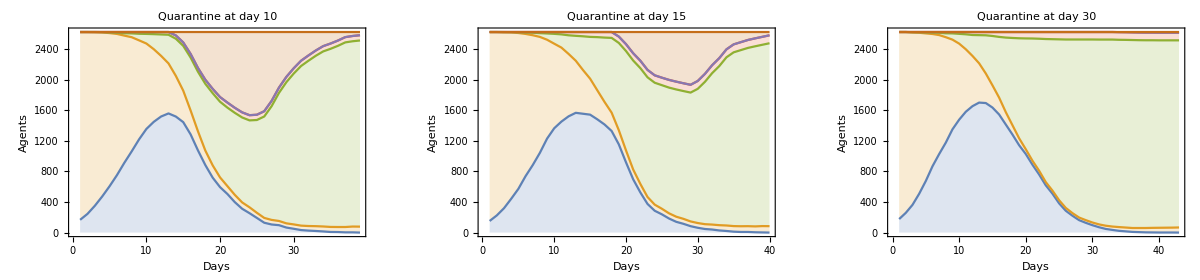

```mathematica
infectionRate=0.4;
symptomaticRate=0.84;

ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5, p,10,citypop,0.0001];
ukNeighbors=agentNeighborhoods [ukSupergraph];
quarantiningIntroduced=10;
Parallelize[
numbers20  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
q4 =sirPlot[numbers20,PlotLabel->"Quarantine at day 10"];
];

quarantiningIntroduced=15;
Parallelize[
numbers21  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
q5 =sirPlot[numbers21,PlotLabel->"Quarantine at day 15"];
];

quarantiningIntroduced=30;
Parallelize[
numbers22  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
q6 =sirPlot[numbers22,PlotLabel->"Quarantine at day 30"];
];

GraphicsRow[{q4, q5, q6}]
```

As expected above, we can see that when quarantine is introduced earlier, there are less infected cases, and an increase in quarantined cases which results in a flattened curve of infection. We would expect that with an earlier quarantine date, there would be a decrease in overall deaths, however, due to the death rate being so low, we cannot visualise the effect a change in when quarantine is introduced affects the amount of deaths. There is also an issue with visualising the accurate number of infected cases, due to symptomatic cases falling into the quarantine curve, so cannot fully assess how quarantine affects the true curve of infections.

Change in Infection Rate (Quarantine at day 15)

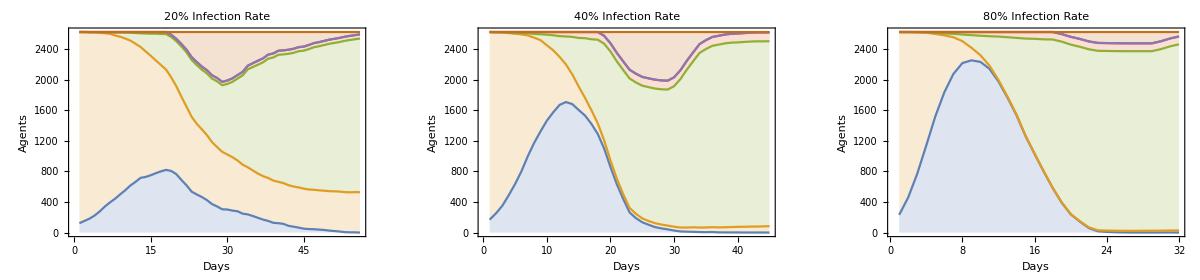

```mathematica
quarantiningIntroduced=15;ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5,p,10,citypop,0.0001];
temp=Join[Keys[Select[measuresDays,MemberQ[#,"Social distancing"]&]],Keys[Select[measuresDays,MemberQ[#,"Public health measures"]&]]];

infectionRate=0.2;
β=Table[infectionRate,{i,maxSteps}];
For[i=1,i≤Length[temp],i++,For[j=0,j<effectDuration&&temp[[i]]+j≤Length[β],j++,β[[temp[[i]]+j]]*=infectionMultiplier;];]
Parallelize[
numbers23  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
i4=sirPlot[numbers23,PlotLabel->"20% Infection Rate"];
];

infectionRate=0.4;
β=Table[infectionRate,{i,maxSteps}];
For[i=1,i≤Length[temp],i++,For[j=0,j<effectDuration&&temp[[i]]+j≤Length[β],j++,β[[temp[[i]]+j]]*=infectionMultiplier;];]
Parallelize[
numbers24 =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
i5=sirPlot[numbers24,PlotLabel->"40% Infection Rate"];
];

infectionRate=0.8;
β=Table[infectionRate,{i,maxSteps}];
For[i=1,i≤Length[temp],i++,For[j=0,j<effectDuration&&temp[[i]]+j≤Length[β],j++,β[[temp[[i]]+j]]*=infectionMultiplier;];]
Parallelize[
numbers25 =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
i6=sirPlot[numbers25,PlotLabel->"80% Infection Rate"];
];

GraphicsRow[{i4,i5,i6}]
```

We have already seen the effect of having a change in infection rate, however, there is another affect when introducing quarantining earlier. We can see that after day 15, the curve of the infection flattens due to infected cases falling into quarantine.

Change in Symptomatic Rate (Quarantine at day 15)

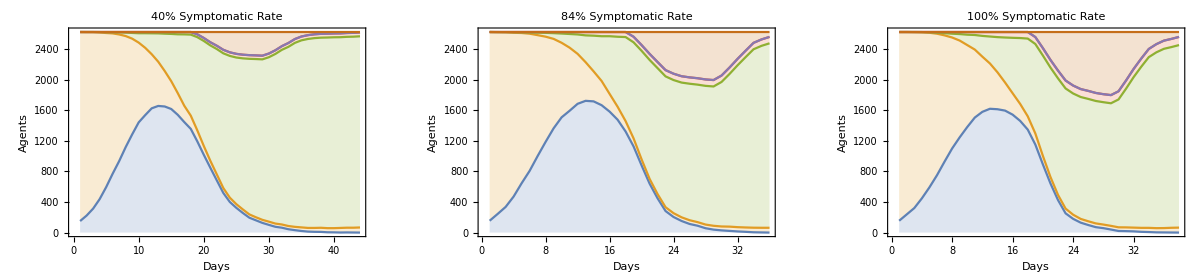

```mathematica
quarantiningIntroduced=15;infectionRate=0.4;symptomaticRate=0.84;
β=Table[infectionRate,{i,maxSteps}];
temp=Join[Keys[Select[measuresDays,MemberQ[#,"Social distancing"]&]],Keys[Select[measuresDays,MemberQ[#,"Public health measures"]&]]];
For[i=1,i≤Length[temp],i++,For[j=0,j<effectDuration&&temp[[i]]+j≤Length[β],j++,β[[temp[[i]]+j]]*=infectionMultiplier;];]
ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5,p,10,citypop,0.0001];
agentNeighborhoods [ukSupergraph];

symptomaticRate=0.4;
Parallelize[
numbers26  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
s4 =sirPlot[numbers26,PlotLabel->"40% Symptomatic Rate"];
]

symptomaticRate=0.84;
Parallelize[
numbers27  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
s5 =sirPlot[numbers27,PlotLabel->"84% Symptomatic Rate"];
]

symptomaticRate=1;
Parallelize[
numbers28 =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
s6 =sirPlot[numbers28,PlotLabel->"100% Symptomatic Rate"];
]

GraphicsRow[{s4, s5, s6}]
```

Now that quarantine has been introduced on day 15, we can see the effect of a higher symptomatic rate on our model. As expected, as the symptomatic rate increases, the more cases there are of people in quarantine.

3x3 Graph Showing the Effect of Changing the Parameters (Quarantine at day 15)

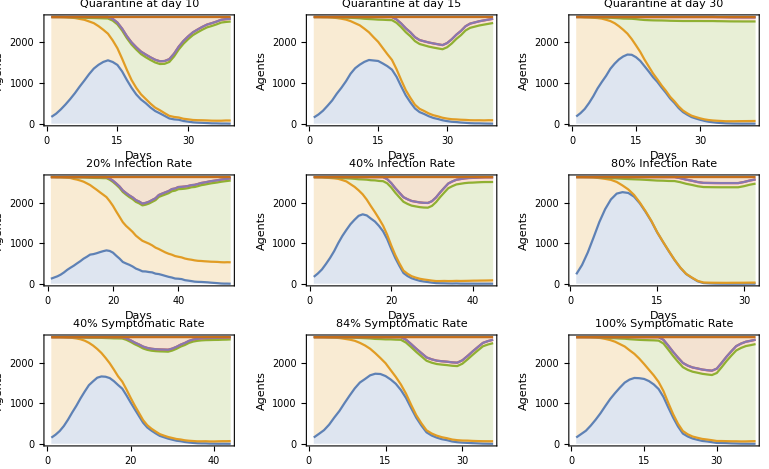

```mathematica
GraphicsGrid[{{q4,q5,q6},{i4,i5,i6},{s4,s5,s6}}]
```

After evaluating these parameters, we have seen there are many limitations that we would hope to change in future work. One main limitation we have come across is the population size of the above graphs. We have found that when assessing a realistic start date of quarantining, our graph has already had its peak in infections due to only having a small population and thus a quicker spread. Another limitation we have is that our symptomatic cases fall into the quarantine section. This is needed for our model to run, however, it makes it extremely difficult to visualise the number of infected cases, as some cases in quarantine are no longer infected. The final main limitation is the number of deaths visible in the model, there are clearly not enough deaths present in our graphs regarding the number of infections, which must be caused by our death rate. 

In understanding our parameters and limitations, our next step is to increase the population size, and use realistic parameters in order to be able to compare our model with real UK data.

How Big Can We Go?

In a hope to fix the limitation of the size of the population, we need to check how big of a population our graph can take. In order to find this out, we can calculate the vertex count of certain Supergraphs.

```mathematica
h1=ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5,p,10,citypop,0.1];
VertexCount[h1]
```

2665459

```mathematica
h2=ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5,p,10,citypop,0.01];
VertexCount[h2]
```

266513

```mathematica
h3=ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5,p,10,citypop,0.001];
VertexCount[h3]
```

26618

```mathematica
h4=ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5,p,10,citypop,0.0005];
VertexCount[h4]
```

13289

We can see that the vertex count is still low for 0.005, but too high for 0.1. In order to compare our model with realistic data, we want to get to the highest feasible population our model will take. After attempting to run the graph with 0.001, Mathematica crashed and unloaded all inputs, therefore we will realistically have to run with the scale factor for population being 0.001.

Comparing UK Supergraph to Real Data

We now want to compare our model with realistic data. To do so we should tune the parameters to the true figures we have by our references. We have that quarantine started on 24th March, therefore ‘quarantineIntroduced=52’, taking the lowest of the infection rates, we will refer to the ‘overnight camp’ study and set ‘infectionRate=0.44’, and our symptomatic rate is accurate so we shall keep that at ‘symptomaticRate=0.84’.

```mathematica
quarantiningIntroduced=52;
initialInfected=1;
infectionRate=0.44;
temp=Join[Keys[Select[measuresDays,MemberQ[#,"Social distancing"]&]],Keys[Select[measuresDays,MemberQ[#,"Public health measures"]&]]];
For[i=1,i≤Length[temp],i++,For[j=0,j<effectDuration&&temp[[i]]+j≤Length[β],j++,β[[temp[[i]]+j]]*=infectionMultiplier;];]
β=Table[infectionRate,{i,maxSteps}];
symptomaticRate=0.84;
ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5,p,10,citypop,0.001];
ukNeighbors=agentNeighborhoods[ukSupergraph];
Parallelize[
numbersM  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
Mix=sirPlot[numbersM,PlotLabel->"Realistic Parameters"];
]
GraphicsRow[{Mix,DLLP}]
```

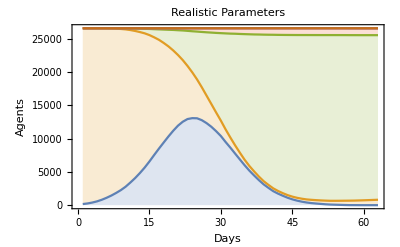

When looking at our SIR graph, although it contains realistic figures which should make it somewhat equivalent to real world figures, we can instantly see that it is not accurate. We have that the infection still peaks long before quarantining is introduced, and hence quarantining will have little effect on reducing the flow of infection. It also seems that there isn’t many deaths which we know to exist from the UK data. It therefore seems very difficult to compart our model with the UK data given. 

In order to have an easier comparison, we can transform our current SIR graph into the same format as the UK data, a logarithmic graph.

```mathematica
temp2=numbersN//Transpose;
confirmedCases=temp2[[1]]+temp2[[6]];
dead=temp2[[4]];
log1=ListLogPlot[{confirmedCases,dead},PlotLegends->{"Confirmed Cases","Dead"},Filling->{1->Bottom,2->Bottom},PlotMarkers->Automatic,ImageSize->300,PlotRange->Full];
GraphicsRow[{log1, DLLP}]
```

-Graphics-

If we take the dates from our graph to be from day 1 to around day 45, and compare it to that of the real data from where the confirmed cases hits 100 on the scale to around mid may (taking the same time frame) we can see extremely similar graphs. Of course, we have to point out the differences with quarantine and the dates of the graph being different, which we will discuss later, however, we can clearly see that our model follows a similar trend to that of real world data. Both the confirmed cases and the death follow an increasing curve until they flatten off. However, this is merely one similarity that we can show our model has with the real world findings. 

There are, however, multiple differences we can see. When quarantining is introduced in our model, at day 52, there is already a decline in confirmed cases, whereas in the real data, quarantining is introduced before the peak, which we can see flattens the curve of infections after it is introduced. When comparing the dates of the graphs we mentioned above, our quarantine was not introduced, whereas in the other graph it was. Another difference is that our graph has the confirmed cases declining from after day 40, and continuing to decline. This is due to having a quick peak of infection in our network due to the smaller population size. This does not happen in the real data, instead there is still a constant but flattened spread of infection. 

Our model clearly has its limitations, which makes comparing it with real data a difficult task, the main still being the size of the population we can model. However, the data we are comparing with also has its limitations, making it difficult to use. We can see that in February, in which both graphs begin, there are anomalies residing in the real data which makes it near impossible to compare that month to our own model. This is clearly an issue due to the fact that with our smaller population size, most of our infections fall into that month. 

Clearly, our model has a similar trend with the real data, however, there is more work to be done in order to get our model to be more accurate.

Extra Work Carried Out in Evaluation and Older Plots

These extra graphs were made before we had the idea to convert our ‘realistic’ graph into a logarithmic graph. When loading our first ‘large’ graph, we saw how different the SIR graph looked compared to what we know to be true, and we knew this was down to the sizing of the population our model could hold. In order to achieve a more realistic looking SIR graph, where quarantine affects the actual flow of infections, we tried to build a large graph with changes to the quarantine and infection rate parameters. However, when transforming our original graph to a logarithmic graph, we realised we did have a common trend and these graphs may not be needed. We just didn’t have the heart to delete them as they took around 10 hours each to load!

Infection rate reduced to 0.25:

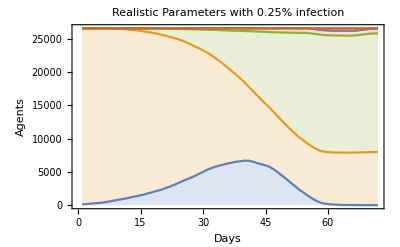

```mathematica
quarantiningIntroduced=52;
initialInfected=1;
infectionRate=0.25;
β=Table[infectionRate,{i,maxSteps}];
temp=Join[Keys[Select[measuresDays,MemberQ[#,"Social distancing"]&]],Keys[Select[measuresDays,MemberQ[#,"Public health measures"]&]]];
For[i=1,i≤Length[temp],i++,For[j=0,j<effectDuration&&temp[[i]]+j≤Length[β],j++,β[[temp[[i]]+j]]*=infectionMultiplier;];]
symptomaticRate=0.84;ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5,p,10,citypop,0.001];
ukNeighbors=agentNeighborhoods [ukSupergraph];
Parallelize[
numbersN  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
Mix2=sirPlot[numbersN,PlotLabel->"Realistic Parameters with 0.25% infection"];
]
GraphicsRow[{Mix2,DLLP}]
```

```mathematica
temp3=numbersO//Transpose;
confirmedCases2=temp3[[1]]+temp3[[6]];
dead2=temp3[[4]];
log2=ListLogPlot[{confirmedCases2,dead2},PlotLegends->{"Confirmed Cases","Dead"},Filling->{1->Bottom,2->Bottom},PlotMarkers->Automatic,ImageSize->300,PlotRange->Full];
GraphicsRow[{log2, DLLP}]
```

-Graphics-

Quarantine introduced at day 25:

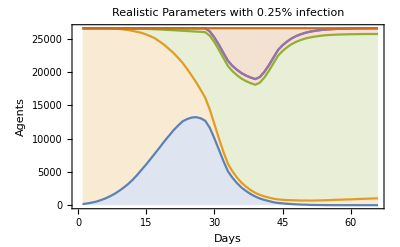

```mathematica
quarantiningIntroduced=25;
initialInfected=1;
infectionRate=0.44;
β=Table[infectionRate,{i,maxSteps}];
temp=Join[Keys[Select[measuresDays,MemberQ[#,"Social distancing"]&]],Keys[Select[measuresDays,MemberQ[#,"Public health measures"]&]]];
For[i=1,i≤Length[temp],i++,For[j=0,j<effectDuration&&temp[[i]]+j≤Length[β],j++,β[[temp[[i]]+j]]*=infectionMultiplier;];]
symptomaticRate=0.84;ukSupergraph = generateSupergraph[IndexGraph@AdjacencyGraph[coupling],5,p,10,citypop,0.001];
ukNeighbors=agentNeighborhoods [ukSupergraph];
Parallelize[
numbersO  =simulateComplete[ukNeighbors, reinfectionRate,vaccinationRate,ageDist, 50, 100];
Mix3=sirPlot[numbersO,PlotLabel->"Realistic Parameters with Quarantining at day 25."];
]
GraphicsRow[{Mix3,DLLP}]
```

```mathematica
temp4=numbersO//Transpose;
confirmedCases3=temp4[[1]]+temp4[[6]];
dead3=temp4[[4]];
log3=ListLogPlot[{confirmedCases3,dead3},PlotLegends->{"Confirmed Cases","Dead"},Filling->{1->Bottom,2->Bottom},PlotMarkers->Automatic,ImageSize->300,PlotRange->Full];
GraphicsRow[{log3, DLLP}]
```

-Graphics-

## Conclusions & Future Work

By adapting the work of [18], we have been able to produce a working model predicting the spread of COVID-19. We have built onto this model by adding in: asymptomatic and symptomatic infection, symptomatic rate, vaccination rate, reinfection rate, quarantining, age distributions, etc. as shown above. When generating our final supergraph, we have been able to compare the results with real data provided at the beginning of our notebook, and have found that our model does in fact follow the trend shown in the data. However, as aforementioned, there are many limitations to our model that we have come across when evaluating the different parameters we use. In future work, we hope to be able to reduce these limitations in order to obtain the most realistic model we can, however, with such a tight timeframe and smaller systems, it is unrealistic to assume we could have attained a model with a true population size and 100% realistic parameters.

One key limitation found in the evaluation was the size of the population our model could handle. Clearly on a normal laptop, Mathematica does not have the capability to produce an accurate model, and therefore, we have not been able to properly compare our model to real life data. To improve in future work, we would hope to be able to put our model onto a Super Computer to see whether it is in fact an accurate representation of the UK data we have, or if it is still inaccurate. We have in fact tried to put our model onto Macleod, but due to IT issues at the University, we were unable to access the cluster over the weekend. Another limitation we found with the population size, is that with all the realistic parameters put into place, we were still witnessing a spike in infection far to quickly in our model. This is due to having a smaller population and hence a quicker spread of the virus. 

Another cause for the spike of infection could be down to the transmission rate of asymptomatic infection. We were unable to find any references to a precise figure to add to our model, although we know through the news and papers online that there seems to be some evidence that asymptomatic infection has a smaller transmission rate compared to symptomatic infection. We did not want to add in parameters which were not backed by scientific data, and therefore did not add this into our model. This could have resulted in a quicker peak of infections in comparison to real data as the overall transmissions would be higher if solely based upon symptomatic transmission rates. In the future, we hope that there will be data backing claims of a smaller transmission rate for asymptomatic infections which we could add into our model to make it more accurate.

To better our model, we could look into the close contacts people have, where if one person contracts COVID-19, the other(s) are likely to get it. We have not delved much into social networks which would give a more precise spread of infection among groups and communities of people. We could also look into the different strains of COVID, adding in the different infection rates, symptomatic rates and deaths. However, these adaptations to our model will be easier to add when there is more evidence to back up articles online. 

Due to the ever-changing nature of the disease we could never have a completely accurate model representing the spread of COVID-19.

## References

[1]  Worldometer. Age, sex, existing conditions of covid-19 cases and deaths. https://www.worldometers.info/coronavirus/coronavirus-age-sex-demographics/.
[2]  GOV.UK. Uk coronavirus data. https://coronavirus.data.gov.uk/.
[3]  Linda  JS  Allen,  Fred  Brauer,  Pauline  Van  den  Driessche,  and  JianhongWu.Mathematical epidemiology - Chapter 2, volume 1945. Springer, 2008.
[4]  Arnoud Buzing.  The sir model for spread of disease, 2020.
[5]  Oyungerel  Byambasuren,  Magnolia  Cardona,  Katy  Bell,  Justin  Clark,Mary-Louise McLaws, and Paul Glasziou. Estimating the extent of asymp-tomatic covid-19 and its potential for community transmission:  systematicreview and meta-analysis.Official  Journal  of  the  Association  of  MedicalMicrobiology and Infectious Disease Canada, 5(4):223–234, 2020
[6]  Jordana  Cepelewicz.   The  hard  lessons  of  modeling  the  coronavirus  pan-demic, 2020.
[7]  European  Centre  for  Disease  Prevention  and  Control.   Transmission  ofcovid-19, 2020.
[8]  Jordan Hasler.  Exploring epidemiological modeling, 2020.
[9]  Stephen A Lauer, Kyra H Grantz, Qifang Bi, Forrest K Jones, Qulu Zheng,Hannah  R  Meredith,  Andrew  S  Azman,  Nicholas  G  Reich,  and  JustinLessler. The incubation period of coronavirus disease 2019 (covid-19) frompublicly reported confirmed cases:  estimation and application.Annals ofinternal medicine, 172(9):577–582, 2020.
[10]  Yang  Liu,  Rosalind  M  Eggo,  and  Adam  J  Kucharski.   Secondary  attackrate and superspreading events for sars-cov-2.The Lancet, 395(10227):e47,2020.
[11]  Emma S McBryde, Michael T Meehan, Oyelola A Adegboye, Adeshina IAdekunle, Jamie M Caldwell, Anton Pak, Diana P Rojas, Bridget Williams,and James M Trauer.  Role of modelling in covid-19 policy development.Paediatric respiratory reviews, 2020.1
[12]  Robert  B.  Nachbar.   Epidemiological  models  for  influenza  and  covid-19,2020.
[13]  Sayak  Roy.   Covid-19  reinfection:   myth  or  truth?SN ComprehensiveClinical Medicine, 2(6):710–713, 2020.
[14]  Marco Thiel.  Simulating a global ebola outbreak, 2014.
[15]  Kelvin  Kai-Wang  To,   Owen  Tak-Yin  Tsang,   Wai-Shing  Leung,   An-thony Raymond Tam, Tak-Chiu Wu, David Christopher Lung, Cyril Chik-Yan Yip, Jian-Piao Cai, Jacky Man-Chun Chan, Thomas Shiu-Hong Chik,et  al.   Temporal  profiles  of  viral  load  in  posterior  oropharyngeal  salivasamples and serum antibody responses during infection by sars-cov-2:  anobservational cohort study.The Lancet Infectious Diseases, 20(5):565–574,2020.
[16]  Robert  Verity,  Lucy  C  Okell,  Ilaria  Dorigatti,  Peter  Winskill,  CharlesWhittaker,  Natsuko  Imai,  Gina  Cuomo-Dannenburg,  Hayley  Thompson,Patrick  GT  Walker,  Han  Fu,  et  al.   Estimates  of  the  severity  of  coron-avirus disease 2019: a model-based analysis.The Lancet infectious diseases,20(6):669–677, 2020.
[17]  Duncan  J  Watts  and  Steven  H  Strogatz.   Collective  dynamics  of  ‘small-world’networks.nature, 393(6684):440–442, 1998.
[18]  Christopher Wolfram.  Agent-based network models for covid-19, 2020.